-30303.

-4545.45

-53475.9

-8021.39

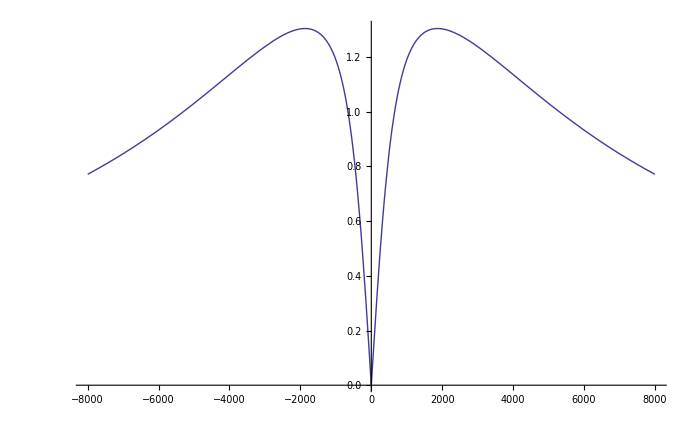

```mathematica
R1=2200;
R2=3300;
C1=100/10^9;
C2=10/10^9;
a=-R2*C1;
b=R2*C2+C1*R1;
c=C1*C2*R1*R2;
roots=s/.Solve[1+b*s+c*s^2==0,s];
α=N[roots[[1]]]
β=N[roots[[2]]]
A = a*α/(α-β)/c
B = a*β/(α-β)/c
Lambda[f_]:=a*I*2*π*f/(1+b*I*2*π*f-c*4*π^2*f^2);
Plot[Abs[Lambda[f]],{f,-8000,8000},PlotRange->All]
```

```mathematica
Apart[a*s/(s-β)/(s-α)/c,s]
Apart[a*s/(1+b*s+c*s^2),s]
```

1500000/(17 (50000+11 s))-30000000/(17 (1000000+33 s))

1500000/(17 (50000+11 s))-30000000/(17 (1000000+33 s))